```mathematica
Solve[{x(1+a(1-x)+k)-p== 0,p>0,a>1,k>0,x>0,(1+a+k)^2-4 a p>0},x]
```

{{x→ConditionalExpression[(1+a+k)/(2 a)-1/2 √((1+2 a+a^2+2 k+2 a k+k^2-4 a p)/a^2),0<p<(1+2 a+a^2+2 k+2 a k+k^2)/(4 a)&&a>1&&k>0]},{x→ConditionalExpression[(1+a+k)/(2 a)+1/2 √((1+2 a+a^2+2 k+2 a k+k^2-4 a p)/a^2),0<p<(1+2 a+a^2+2 k+2 a k+k^2)/(4 a)&&a>1&&k>0]}}

```mathematica
Simplify[Solve[D[p(1-(1+a+k-√((1+a+k)^2-4 a p))/(2 a))-k^2,p]== 0,p]]
```

{{p→(1+a^2+2 k+k^2+4 a (1+k)-√((1-a+k)^2 (a^2+a (1+k)+(1+k)^2)))/(9 a)},{p→(1+a^2+2 k+k^2+4 a (1+k)+√((1-a+k)^2 (a^2+a (1+k)+(1+k)^2)))/(9 a)}}

```mathematica
Limit[p(1-(1+a+k-√((1+a+k)^2-4 a p))/(2 a))-k^2,p-> { (1+a^2+2 k+k^2+4 a (1+k)+√((1-a+k)^2 (a^2+a (1+k)+(1+k)^2)))/(9 a),(1+a^2+2 k+k^2+4 a (1+k)-√((1-a+k)^2 (a^2+a (1+k)+(1+k)^2)))/(9 a)}]
```

Limit[-k^2+p (1-(1+a+k-√((1+a+k)^2-4 a p))/(2 a)),p→{(1+a^2+2 k+k^2+4 a (1+k)+√((1-a+k)^2 (a^2+a (1+k)+(1+k)^2)))/(9 a),(1+a^2+2 k+k^2+4 a (1+k)-√((1-a+k)^2 (a^2+a (1+k)+(1+k)^2)))/(9 a)}]

```mathematica
N[Solve[Limit[D[-k^2+((1+a^2+2 k+k^2+4 a (1+k)+√((1-a+k)^2 (a^2+a (1+k)+(1+k)^2))) (-3+3 a-3 k+√(5+5 a^2+10 k+5 k^2+2 a (1+k)-4 √((1-a+k)^2 (a^2+a (1+k)+(1+k)^2)))))/(54 a^2),k],a-> 0.2]== 0,k]]
```

$Aborted

```mathematica
N[Solve[1/54 (-108 k+(6+6 k+k^2-√(k^2 (3+3 k+k^2))) (-3+(6+5 k+(k (6+9 k+4 k^2))/(√(k^2 (3+3 k+k^2))))/(√(12 k+5 k^2+4 (3+√(k^2 (3+3 k+k^2))))))+(6+2 k-(k (6+9 k+4 k^2))/(2 √(k^2 (3+3 k+k^2)))) (-3 k+√(12 k+5 k^2+4 (3+√(k^2 (3+3 k+k^2))))))== 0,k]]
```

{{k→0.122392-1.18424×10^-15 ⅈ},{k→-1.49742-0.86745 ⅈ},{k→-1.49742+0.86745 ⅈ}}

```mathematica
Plot3D[((1+a^2+2 k+k^2+4 a (1+k)-√((1-a+k)^2 (a^2+a (1+k)+(1+k)^2))) (-3+3 a-3 k+√(5+5 a^2+10 k+5 k^2+2 a (1+k)+4 √((1-a+k)^2 (a^2+a (1+k)+(1+k)^2)))))/(54 a^2)-k^2,{a,0,4},{k,0,0.5},PlotTheme->"Monochrome",AxesLabel->{Style[α,Bold,16],Style[k,Bold,16],Style[π,Bold,16]},Ticks->{{0,1,3},{0,1/8,1/5},Automatic}]
```

-Graphics3D-

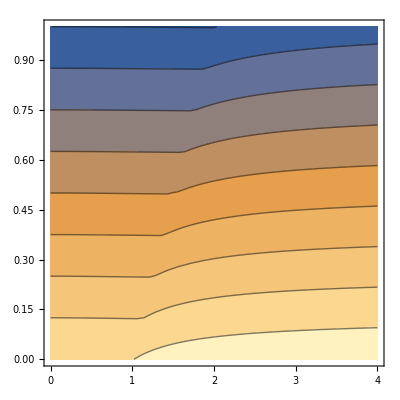

```mathematica
ContourPlot[-2 k+((2+4 a+2 k-((1-a+k)^2 (a+2 (1+k))+2 (1-a+k) (a^2+a (1+k)+(1+k)^2))/(2 √((1-a+k)^2 (a^2+a (1+k)+(1+k)^2)))) (-3+3 a-3 k+√(5+5 a^2+10 k+5 k^2+2 a (1+k)+4 √((1-a+k)^2 (a^2+a (1+k)+(1+k)^2)))))/(54 a^2)+((1+a^2+2 k+k^2+4 a (1+k)-√((1-a+k)^2 (a^2+a (1+k)+(1+k)^2))) (-3+(10+2 a+10 k+(2 ((1-a+k)^2 (a+2 (1+k))+2 (1-a+k) (a^2+a (1+k)+(1+k)^2)))/(√((1-a+k)^2 (a^2+a (1+k)+(1+k)^2))))/(2 √(5+5 a^2+10 k+5 k^2+2 a (1+k)+4 √((1-a+k)^2 (a^2+a (1+k)+(1+k)^2))))))/(54 a^2),{a,0,4},{k,0,1}]
```